```mathematica
(***Note: Values for generating these plots are embedded within the raw data set, which is too large to upload onto the public data repository***)
```

```mathematica
(****V1 axons***)
```

```mathematica
dateMouseSessionListV1={{"061222","Mouse22565","Session1"},{"061222","Mouse22565","Session2"},{"061222","Mouse22582","Session1"},{"061222","Mouse22582","Session2"},{"061422","Mouse22565","Session1"},{"061522","Mouse22582","Session1"},{"072622","Mouse23049","Session1"},{"072522","Mouse23090","Session1"},{"072822","Mouse23049","Session1"},{"072822","Mouse23004","Session1"},{"072922","Mouse23004","Session1"},{"080222","Mouse23049","Session1"}};
```

```mathematica
ratesPMV1=Flatten[Table[numROIsCBs=Length[FileNames["*",File[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListV1[[n,1]],"/",dateMouseSessionListV1[[n,2]],"/",dateMouseSessionListV1[[n,3]],"/dFOverF0TimeSeries_CellBodies/"]]]];ToExpression/@Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListV1[[n,1]],"/",dateMouseSessionListV1[[n,2]],"/",dateMouseSessionListV1[[n,3]],"/","MeanInferredFiringRates/",dateMouseSessionListV1[[n,1]],"_",dateMouseSessionListV1[[n,2]],"_",dateMouseSessionListV1[[n,3]],"_meanFR_cellBody",ToString[cellBody],".txt"]],{cellBody,1,numROIsCBs}],{n,1,Length[dateMouseSessionListV1]}]];
```

```mathematica
ratesV1=Flatten[Table[numROIsAxons=Length[FileNames["*",File[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListV1[[n,1]],"/",dateMouseSessionListV1[[n,2]],"/",dateMouseSessionListV1[[n,3]],"/dFOverF0TimeSeries_Axons/"]]]];ToExpression/@Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListV1[[n,1]],"/",dateMouseSessionListV1[[n,2]],"/",dateMouseSessionListV1[[n,3]],"/","MeanInferredFiringRates/",dateMouseSessionListV1[[n,1]],"_",dateMouseSessionListV1[[n,2]],"_",dateMouseSessionListV1[[n,3]],"_meanFR_axon",ToString[axon],".txt"]],{axon,1,numROIsAxons}],{n,1,Length[dateMouseSessionListV1]}]];
```

```mathematica
(****LM axons***)
```

```mathematica
dateMouseSessionListLM={{"060722","Mouse22576","Session1"},{"060722","Mouse22576","Session2"},{"061522","Mouse22576","Session1"},{"062222","Mouse22577","Session1"},{"062822","Mouse23076","Session1"},{"072122","Mouse23076","Session1"},{"062222","Mouse22518","Session1"},{"062322","Mouse22518","Session1"}};
```

```mathematica
ratesPMLM=Flatten[Table[numROIsCBs=Length[FileNames["*",File[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListLM[[n,1]],"/",dateMouseSessionListLM[[n,2]],"/",dateMouseSessionListLM[[n,3]],"/dFOverF0TimeSeries_CellBodies/"]]]];ToExpression/@Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListLM[[n,1]],"/",dateMouseSessionListLM[[n,2]],"/",dateMouseSessionListLM[[n,3]],"/","MeanInferredFiringRates/",dateMouseSessionListLM[[n,1]],"_",dateMouseSessionListLM[[n,2]],"_",dateMouseSessionListLM[[n,3]],"_meanFR_cellBody",ToString[cellBody],".txt"]],{cellBody,1,numROIsCBs}],{n,1,Length[dateMouseSessionListLM]}]];
```

```mathematica
ratesLM=Flatten[Table[numROIsAxons=Length[FileNames["*",File[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListLM[[n,1]],"/",dateMouseSessionListLM[[n,2]],"/",dateMouseSessionListLM[[n,3]],"/dFOverF0TimeSeries_Axons/"]]]];ToExpression/@Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListLM[[n,1]],"/",dateMouseSessionListLM[[n,2]],"/",dateMouseSessionListLM[[n,3]],"/","MeanInferredFiringRates/",dateMouseSessionListLM[[n,1]],"_",dateMouseSessionListLM[[n,2]],"_",dateMouseSessionListLM[[n,3]],"_meanFR_axon",ToString[axon],".txt"]],{axon,1,numROIsAxons}],{n,1,Length[dateMouseSessionListLM]}]];
```

```mathematica
(****LP axons***)
```

```mathematica
dateMouseSessionListLP={{"062222","Mouse22597","Session1"},{"062222","Mouse22597","Session2"},{"072122","Mouse23087","Session1"},{"072122","Mouse23096","Session1"},{"072122","Mouse23096","Session2"},{"073022","Mouse23087","Session1"},{"080122","Mouse23079","Session1"},{"080222","Mouse23079","Session1"},{"080122","Mouse23060","Session1"},{"080222","Mouse23060","Session1"}};
```

```mathematica
ratesPMLP=Flatten[Table[numROIsCBs=Length[FileNames["*",File[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListLP[[n,1]],"/",dateMouseSessionListLP[[n,2]],"/",dateMouseSessionListLP[[n,3]],"/dFOverF0TimeSeries_CellBodies/"]]]];ToExpression/@Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListLP[[n,1]],"/",dateMouseSessionListLP[[n,2]],"/",dateMouseSessionListLP[[n,3]],"/","MeanInferredFiringRates/",dateMouseSessionListLP[[n,1]],"_",dateMouseSessionListLP[[n,2]],"_",dateMouseSessionListLP[[n,3]],"_meanFR_cellBody",ToString[cellBody],".txt"]],{cellBody,1,numROIsCBs}],{n,1,Length[dateMouseSessionListLP]}]];
```

```mathematica
ratesLP=Flatten[Table[numROIsAxons=Length[FileNames["*",File[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListLP[[n,1]],"/",dateMouseSessionListLP[[n,2]],"/",dateMouseSessionListLP[[n,3]],"/dFOverF0TimeSeries_Axons/"]]]];ToExpression/@Table[Import[StringJoin["S:/Imaging/Garrett/FMB208_2PRig/",dateMouseSessionListLP[[n,1]],"/",dateMouseSessionListLP[[n,2]],"/",dateMouseSessionListLP[[n,3]],"/","MeanInferredFiringRates/",dateMouseSessionListLP[[n,1]],"_",dateMouseSessionListLP[[n,2]],"_",dateMouseSessionListLP[[n,3]],"_meanFR_axon",ToString[axon],".txt"]],{axon,1,numROIsAxons}],{n,1,Length[dateMouseSessionListLP]}]];
```

```mathematica
(****************************)
```

```mathematica
ratesPM=Join[ratesPMV1,ratesPMLM,ratesPMLP];
```

```mathematica
v1Color=RGBColor["#ff1f5b"];
```

```mathematica
lpColor=RGBColor["#009ade"];
```

```mathematica
lmColor=RGBColor["#f28522"];
```

```mathematica
v2mColor=Purple;
```

```mathematica
(**********************)
```

```mathematica
v1AxonCharts=Show[BoxWhiskerChart[ratesV1,{{"Whiskers", Directive[Darker@v1Color,Thick]}, {"Fences", Directive[Darker@v1Color,Thick]},{"MedianMarker", Directive[Darker@v1Color,Thickness[0.009]]}},PlotRange->{All,{0,11.2}},ChartStyle->Directive[v1Color,Opacity[0.3]],Frame->False],DistributionChart[ratesV1,PlotRange->{All,{0,11.2}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],v1Color],Frame->False],FrameTicks->{{LinTicks[0,11.2,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lmAxonCharts=Show[BoxWhiskerChart[ratesLM,{{"Whiskers", Directive[Darker@lmColor,Thick]}, {"Fences", Directive[Darker@lmColor,Thick]},{"MedianMarker", Directive[Darker@lmColor,Thickness[0.009]]}},PlotRange->{All,{0,11.2}},ChartStyle->Directive[lmColor,Opacity[0.3]],Frame->False],DistributionChart[ratesLM,PlotRange->{All,{0,11.2}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lmColor],Frame->False],FrameTicks->{{LinTicks[0,11.2,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
lpAxonCharts=Show[BoxWhiskerChart[ratesLP,{{"Whiskers", Directive[Darker@lpColor,Thick]}, {"Fences", Directive[Darker@lpColor,Thick]},{"MedianMarker", Directive[Darker@lpColor,Thickness[0.009]]}},PlotRange->{All,{0,11.2}},ChartStyle->Directive[lpColor,Opacity[0.3]],Frame->False],DistributionChart[ratesLP,PlotRange->{All,{0,11.2}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],lpColor],Frame->False],FrameTicks->{{LinTicks[0,11.2,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
v2mAxonCharts=Show[BoxWhiskerChart[ratesPM,{{"Whiskers", Directive[Darker@v2mColor,Thick]}, {"Fences", Directive[Darker@v2mColor,Thick]},{"MedianMarker", Directive[Darker@v2mColor,Thickness[0.009]]}},PlotRange->{All,{0,11.2}},ChartStyle->Directive[v2mColor,Opacity[0.3]],Frame->False],DistributionChart[ratesPM,PlotRange->{All,{0,11.2}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],v2mColor],Frame->False],FrameTicks->{{LinTicks[0,11.2,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Transparent,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
transp=Show[BoxWhiskerChart[ratesPM,{{"Whiskers", Directive[Transparent,Thick]}, {"Fences", Directive[Transparent,Thick]},{"MedianMarker", Directive[Transparent,Thickness[0.009]]}},PlotRange->{All,{0,11.2}},ChartStyle->Transparent,Frame->False],DistributionChart[ratesPM,PlotRange->{All,{0,11.2}},ChartStyle->Directive[EdgeForm[Transparent],Opacity[0.2],Transparent],Frame->False],FrameTicks->{{LinTicks[0,11.2,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Axes->False,TicksStyle->Thick,FrameStyle->Directive[Black,Thick],Frame->{{True,None},{None,None}},FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

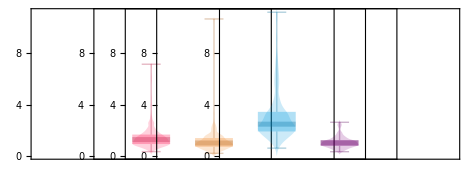

```mathematica
GraphicsRow[{v1AxonCharts,lmAxonCharts,lpAxonCharts,v2mAxonCharts,transp},Spacings->{{-280,-280,-280,-280,-480}}]
```